```mathematica
Exit
```

```mathematica
parseFarField[arg_,ratio_,i_]:=Module[{cy,cx,rx,ry},
{cx,cy}=(({fx[[i]],fy[[i]]}+(3/2*size*padRatio))/(3*size*padRatio)*Dimensions[meta]*padRatio)//Round;
(*cx=cx+RandomInteger[{-3,3}];
cy=cy+RandomInteger[{-3,3}];*)
{rx,ry}=(ratio*Dimensions[meta]*padRatio)//Round;
farField[arg][[cy-ry;;cy+ry,cx-rx;;cx+rx]]
]
centerY[arg_]:=Total[arg*Table[j,{j,Dimensions[arg][[1]]},{i,Dimensions[arg][[2]]}],2]/Total[arg,2];
centerX[arg_]:=Total[arg*Table[i,{j,Dimensions[arg][[1]]},{i,Dimensions[arg][[2]]}],2]/Total[arg,2];

centerIntensity[arg_,ref_:None]:=Module[{cy,cx},
If[ref==None,
{cy,cx}={centerY[arg],centerX[arg]};,
,
{cy,cx}={centerY[ref],centerX[ref]};
];
index=Outer[arg[[Abs[#1[cy]],Abs[#2[cx]]]]&,{Floor,Ceiling},{Floor,Ceiling}];
areaRatio=Outer[Abs[#1[cy]-cy]*Abs[#2[cx]-cx]&,{Floor,Ceiling},{Floor,Ceiling}];
Total[index*areaRatio,2]
];

parseImage[img_,{x_,y_},{w_,h_}]:=Module[{mx=3,my=3,dy,dx},
{dy,dx}={Floor[h/my],Floor[w/mx]};
Outer[img[[y+#1*dy;;y+(#1+1)*dy, x+#2*dx;;x+(#2+1)*dx]]&,Range[0,my-1],Range[0,mx-1]]//Flatten[#,{{1,2},{3},{4}}]&
];

barPlot3D[arg_]:=Module[{ny,nx,p1,p2},
{ny,nx}=Dimensions[arg];
p1={Table[j,{j,ny},{i,nx}],Table[i,{j,ny},{i,nx}],ConstantArray[0,{ny,nx}]}//Transpose[#,{3,1,2}]&//Flatten[#,1]&;
p2={Table[j+1,{j,ny},{i,nx}],Table[i+1,{j,ny},{i,nx}],arg}//Transpose[#,{3,1,2}]&//Flatten[#,1]&;
Graphics3D[Cuboid[#[[1]],#[[2]]]&/@({p1,p2}ᵀ),Axes->True,
BoxRatios->{1,1,1},ViewPoint->{2, -0.5, 2},PlotRange->{All,All,{0,1}}]
];
```

```mathematica
T2=({{-1, 1, 1, 1, 1, 1, 0, 0, 0}, {1, -1, 1, 1, 1, 0, 1, 0, 0}, {1, 1, -1, 1, 0, 0, 0, 0, 1}, {1, 1, 1, -1, 1, 0, 0, 1, 0}, {1, 1, 0, 1, -1, -1, -1, -1, -1}, {1, 0, 0, 0, -1, -ⅈ, 1, 1, ⅈ}, {0, 1, 0, 0, -1, 1, -1, -1, 1}, {0, 0, 0, 1, -1, 1, -1, -1, 1}, {0, 0, 1, 0, -1, ⅈ, 1, 1, -ⅈ}});
testFarField=ArrayReshape[IdentityMatrix[9],{3,3,3,3}];
testGrover={{({{-1, 1, 0}, {1, 1, 0}, {0, 0, 0}}),({{1, -1, 0}, {1, 1, 0}, {0, 0, 0}}),({{1, 1, 0}, {-1, 1, 0}, {0, 0, 0}}),({{1, 1, 0}, {1, -1, 0}, {0, 0, 0}})}};
testQFT={{({{0, 0, 0}, {0, 1, 1}, {0, 1, 1}}),({{0, 0, 0}, {0, 1, -ⅈ}, {0, -1, ⅈ}}),({{0, 0, 0}, {0, 1, -1}, {0, 1, -1}}),({{0, 0, 0}, {0, 1, ⅈ}, {0, -1, -ⅈ}})}};
testCNOT={{({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}}),({{0, 0, 0}, {0, 0, 0}, {1, 0, 0}}),({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}}),({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}})}};
```

```mathematica
p=0.31 2;
size=32p;
λ=0.810;
θx=10Degree;
θy=10Degree;
f=150;
padRatio=10;
```

```mathematica
SetDirectory[NotebookDirectory[]]
Import["./lens-array.m"]
```

/home/stnav/Projects/jensen-lab-mathematica/lens-array

Sample size in um:   {19.84,19.84}

Sample size in pixel:   {32,32}

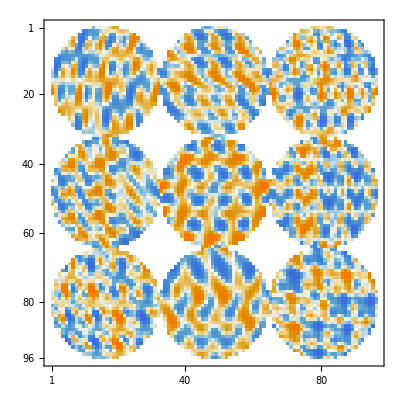

```mathematica
eLocalLens[i_] := 
Sum[T2[[j]][[i]]* Exp[-ⅈ k0√(Outer[Plus,(y-y0[[i]])^2,(x-x0[[i]])^2]+(f^2+fy[[j]]^2+fx[[j]]^2))
+ⅈ Outer[Plus,ky[[j]](y-y0[[i]]),kx[[j]](x-x0[[i]])]]*ellipticalMask,{j,9}];
farField[arg_]:=forwardPropagate[ArrayPad[eGlobalInput[arg]*meta,({{pady}, {padx}})],f, {p, p}]//Abs[#]^2&;
meta=eGlobalLens[({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})];
meta//MatrixPlot
```

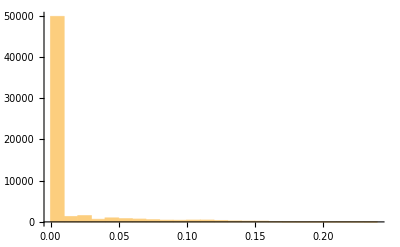

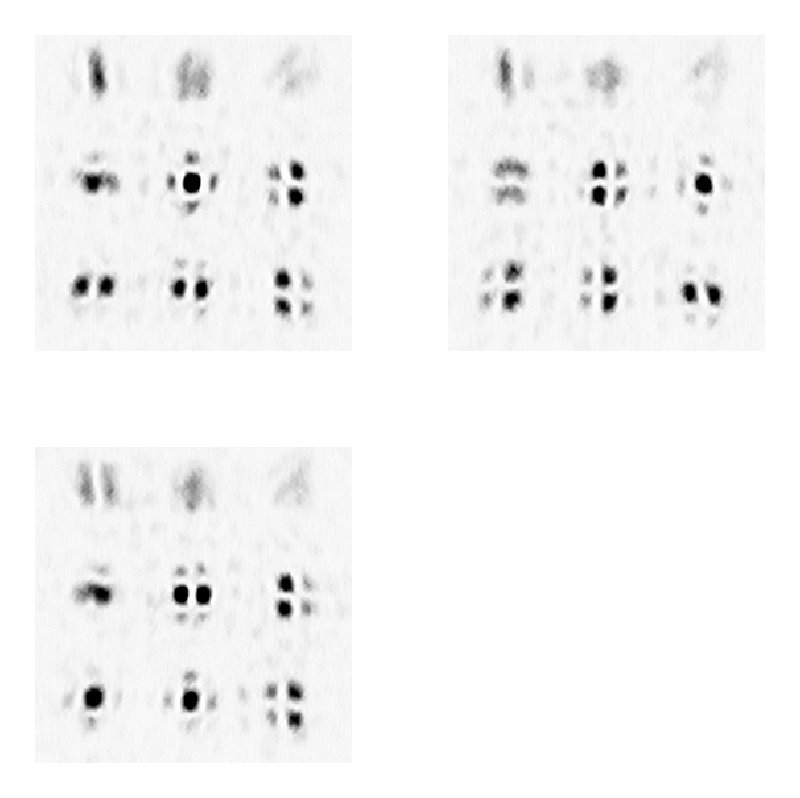

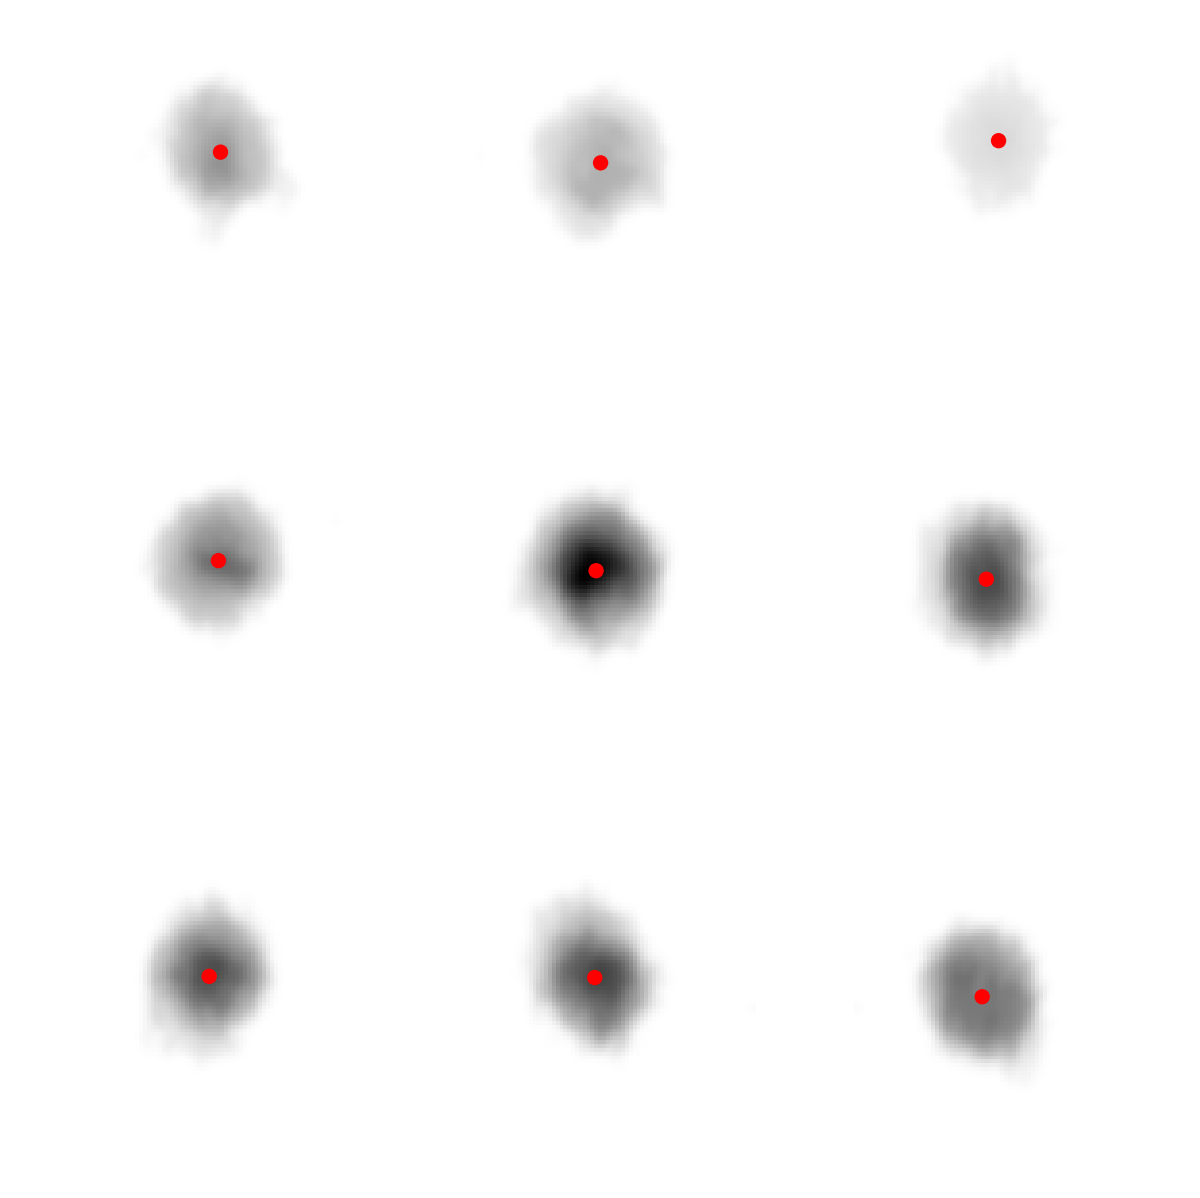

(-Graphics3D- | -Graphics3D-)

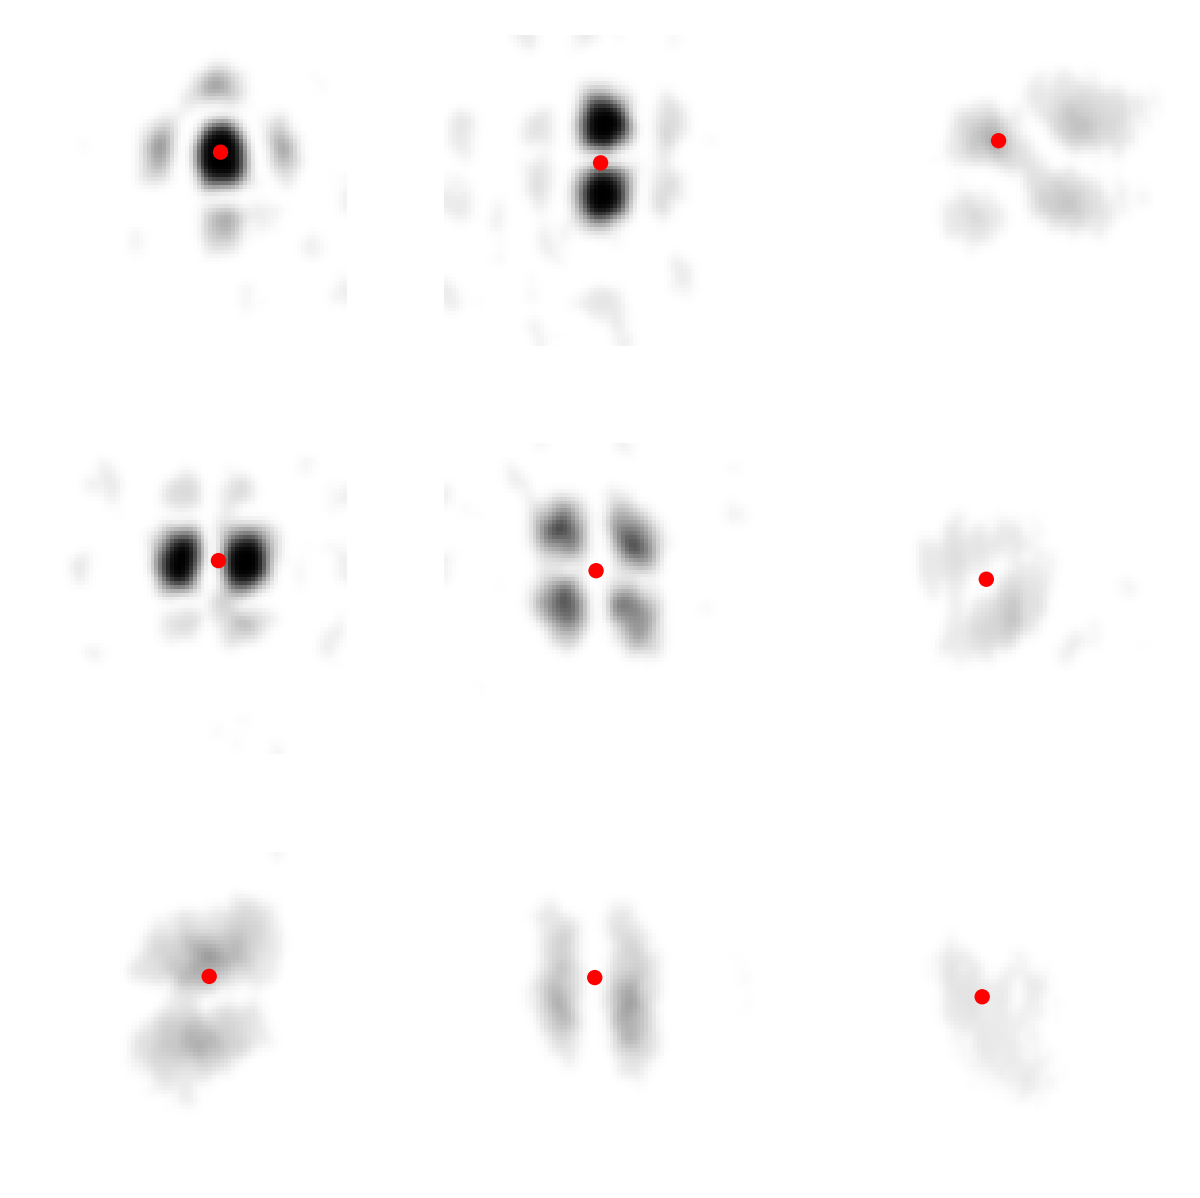

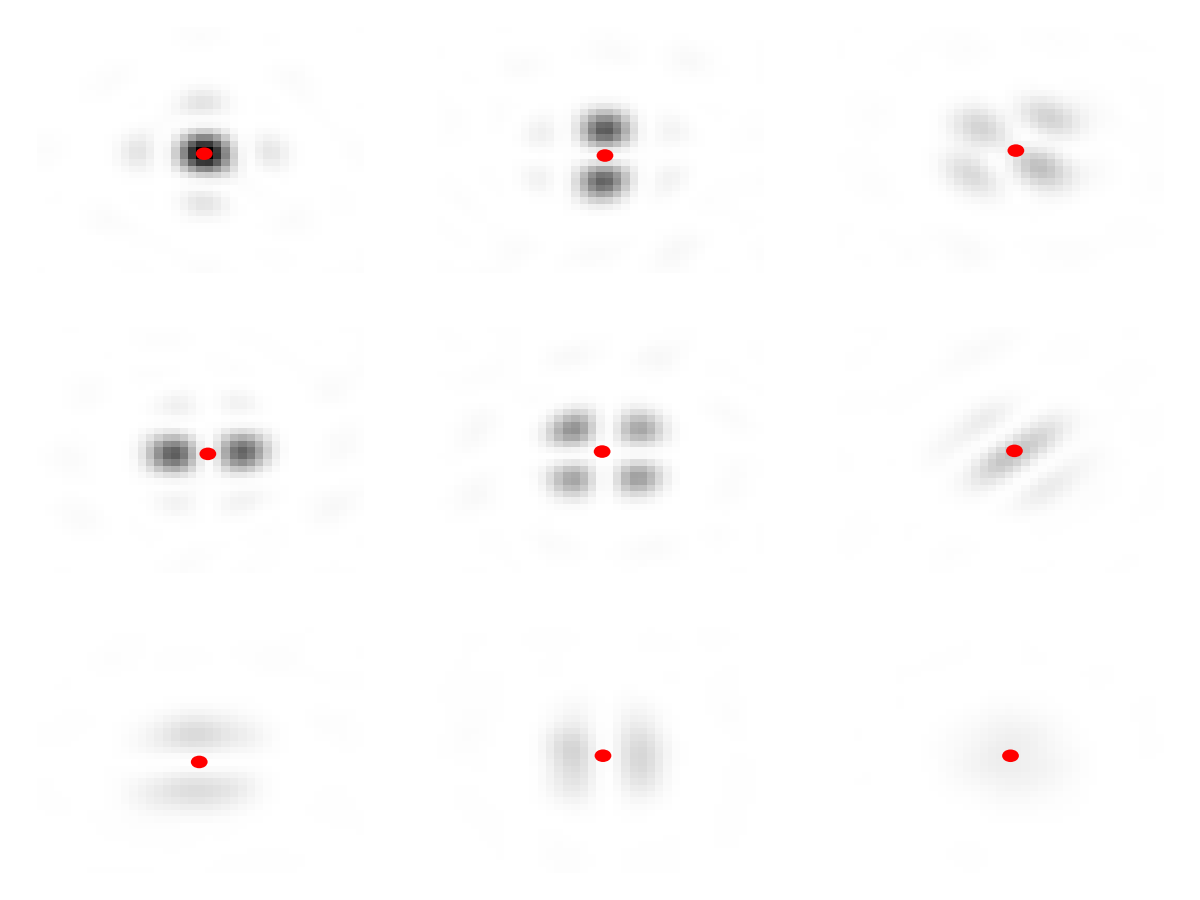
(-Graphics-)

```mathematica
SetDirectory["/mnt/HDD1/Data/JensenLab/2022-10-7, Heralding Lens Array/"];

namesRef={"k1","k2","k3","k4","k5","k6","k7","k8","k9"}//(StringJoin[#,".png"]&)/@#&;

namesRef={"k5","k6","k8","k9"}//(StringJoin[#,".png"]&)/@#&;
(*
namesRef={"k1","k2","k4","k5"}//(StringJoin[#,".png"]&)/@#&;*)

img = Import["grover1.png"]//ColorConvert[#,"Grayscale"]&//ImageData;
test=testGrover[[1]][[1]];

(*ref=Import/@namesRef//(ColorConvert[#,"Grayscale"]&)/@#&//(ImageData)/@#&//Mean;*)
ref=(Import/@namesRef)//(ColorConvert[#,"Grayscale"]&)/*ImageData/*(Threshold[#,0.07]&)/@#&//Mean;
dataRef = parseImage[ref,{360,150},{240,240}]//(GaussianFilter[#,3]&)/@#&;
data = parseImage[img,{360,150},{240,240}]//Threshold[#,0.07]&//(GaussianFilter[#,3]&)/@#&;
dataTest = parseFarField[test,0.02,#]&/@Range[9]//(GaussianFilter[#,1]&)/@#&;

(*(ArrayPlot[#,Frame->False, PlotRange->{All,All,0.5}])&@*ImageData@*(ColorConvert[#,"Grayscale"]&)@*Import@*(StringJoin["cropped-",#]&)/@namesRef//ArrayReshape[#,{3,3}]&//GraphicsGrid*)

parseImage[ref,{360,150},{240,240}]//Flatten//Histogram[#,PlotRange->Full]&

(ArrayPlot[#,Frame->False,PlotRange->{All,All,1}])&@*ImageData@*(ColorConvert[#,"Grayscale"]&)@*Import@*(StringJoin["cropped-qft",#,".png"]&)@*ToString/@{1,2,3,4}//ArrayReshape[#,{2,2}]&//GraphicsGrid

ArrayPlot[#[[2]],Epilog->{Red, Disk[{centerX[#[[2]]]-0.5,Dimensions[#[[2]]][[1]]-centerY[#[[2]]]+0.5}, 2]},PlotRange->Max[dataRef], Frame->False]&/@({data,dataRef}ᵀ)//ArrayReshape[#,{3,3}]&//GraphicsGrid

{{barPlot3D[centerIntensity[#[[1]],#[[2]]]&/@({data,dataRef}ᵀ)//Normalize//ArrayReshape[#,{3,3}]&],barPlot3D[centerIntensity/@dataTest//Normalize//ArrayReshape[#,{3,3}]&]}}//MatrixForm

ArrayPlot[#[[1]],Epilog->{Red, Disk[{centerX[#[[2]]]-0.5,Dimensions[#[[2]]][[1]]-centerY[#[[2]]]+0.5}, 2]},PlotRange->Max[data], Frame->False]&/@({data,dataRef}ᵀ)//ArrayReshape[#,{3,3}]&//GraphicsGrid

ArrayPlot[#[[1]],Epilog->{Red,Disk[{centerX[#[[1]]]-0.5,Dimensions[#[[1]]][[1]]-centerY[#[[1]]]+0.5},1]},PlotRange->Max[dataTest]]&/@({dataTest}ᵀ)//ArrayReshape[#,{3,3}]&//MatrixForm
```

```mathematica
SetDirectory["/mnt/HDD1/Data/JensenLab/2022-10-7, Heralding Lens Array/"];
namesRef={"k1","k2","k3","k4","k5","k6","k7","k8","k9"}//(StringJoin[#,".png"]&)/@#&;
(*namesRef={"k5","k6","k8","k9"}//(StringJoin[#,".png"]&)/@#&;*)
(*namesRef={"k1","k2","k4","k5"}//(StringJoin[#,".png"]&)/@#&;*)


setRef:=(
Echo[namesRef];
ref=(Import/@namesRef)//(ColorConvert[#,"Grayscale"]&)/*ImageData/*(Threshold[#,0.07]&)/@#&//Mean;
dataRef = parseImage[ref,{360,150},{240,240}]//(GaussianFilter[#,3]&)/@#&;
);

sim[{prefix_,testList_,index_}]:=Module[{img,data, test, dataTest},
img = Import[StringJoin[prefix, ToString[index],".png"]]//ColorConvert[#,"Grayscale"]&//ImageData;
test=testList[[index]];
data = parseImage[img,{360,150},{240,240}]//Threshold[#,0.07]&//(GaussianFilter[#,3]&)/@#&;
dataTest = parseFarField[test,0.02,#]&/@Range[9]//(GaussianFilter[#,1]&)/@#&;
{barPlot3D[centerIntensity[#[[1]],#[[2]]]&/@({data,dataRef}ᵀ)//Normalize//ArrayReshape[#,{3,3}]&],
barPlot3D[centerIntensity/@dataTest//Normalize//ArrayReshape[#,{3,3}]&],
((centerIntensity[#[[1]],#[[2]]]&/@({data,dataRef}ᵀ)//Normalize) - (centerIntensity/@dataTest//Normalize))//√(Total[#^2]/Length[#])&
}
]
```

```mathematica
Echo["FarField"];
namesRef={"k1","k2","k3","k4","k5","k6","k7","k8","k9"}//(StringJoin[#,".png"]&)/@#&;
setRef;
(sim[{"k",testFarField//Flatten[#,{1,2}]&,#}]&)/@Range[9]//ArrayReshape[#,{9,3}]&//Transpose//GraphicsGrid

Echo["Grover"];
(*namesRef={"k1","k2","k3","k4","k5","k6","k7","k8","k9"}//(StringJoin[#,".png"]&)/@#&;*)
namesRef={"k1","k2","k4","k5"}//(StringJoin[#,".png"]&)/@#&;
setRef;
(sim[{"grover",testGrover[[1]],#}]&)/@{1,2,3,4}//ArrayReshape[#,{4,3}]&//Transpose//GraphicsGrid

Echo["QFT"];
(*namesRef={"k1","k2","k3","k4","k5","k6","k7","k8","k9"}//(StringJoin[#,".png"]&)/@#&;*)
namesRef={"k5","k6","k8","k9"}//(StringJoin[#,".png"]&)/@#&;
setRef;
(sim[{"qft",testQFT[[1]],#}]&)/@{1,2,3,4}//ArrayReshape[#,{4,3}]&//Transpose//GraphicsGrid
```

FarField

{k1.png,k2.png,k3.png,k4.png,k5.png,k6.png,k7.png,k8.png,k9.png}

-Graphics-

Grover

{k1.png,k2.png,k4.png,k5.png}

-Graphics-

QFT

{k5.png,k6.png,k8.png,k9.png}

-Graphics-

```mathematica
ClearAll[img, data, test, dataTest]
```

{k5.png,k6.png,k8.png,k9.png}

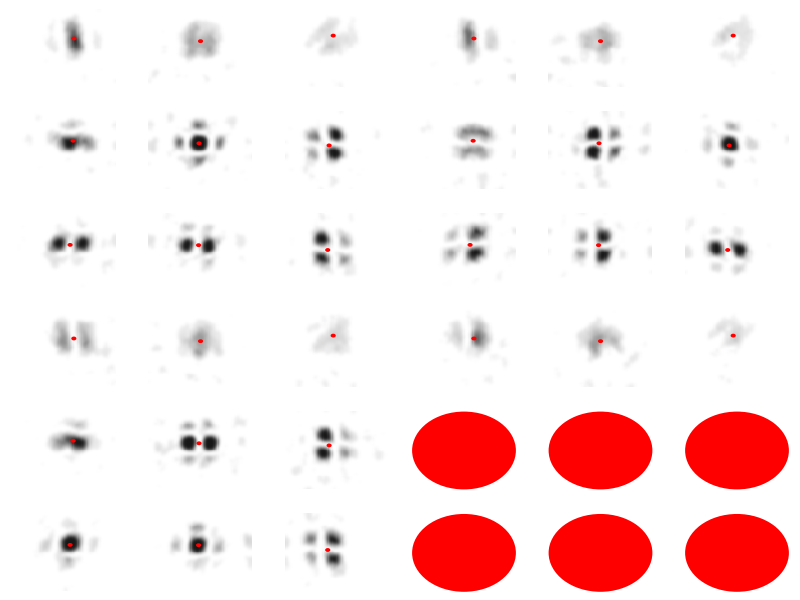
(-Graphics-)

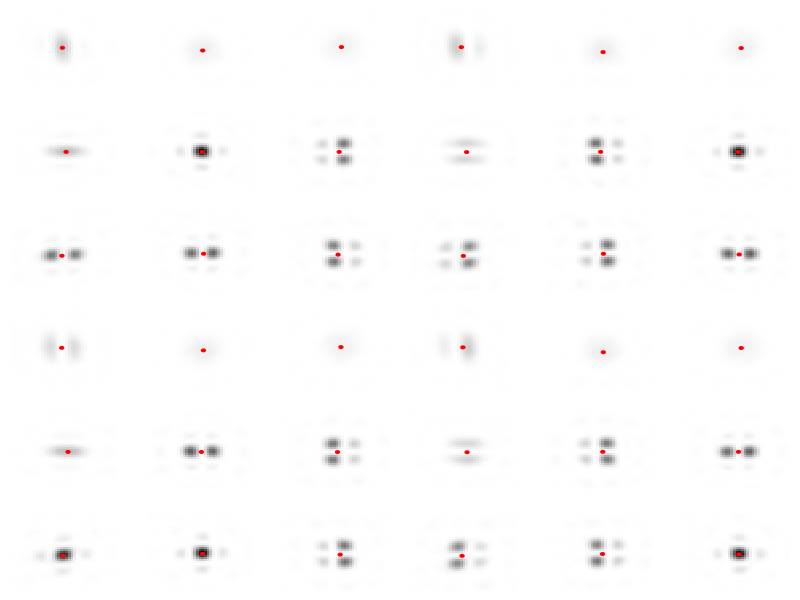
(-Graphics-)

```mathematica
namesRef={"k1","k2","k3","k4","k5","k6","k7","k8","k9"}//(StringJoin[#,".png"]&)/@#&;
namesRef={"k5","k6","k8","k9"}//(StringJoin[#,".png"]&)/@#&;
setRef;

img[i_] := Import[StringJoin["qft",ToString[i],".png"]]//ColorConvert[#,"Grayscale"]&//ImageData;
data[i_]:= parseImage[img[i],{360,150},{240,240}]//Threshold[#,0.07]&//(GaussianFilter[#,3]&)/@#&;
test[i_]:=testQFT[[1]][[i]];
dataTest[i_]:= parseFarField[test[i],0.02,#]&/@Range[9]//(GaussianFilter[#,1]&)/@#&;

plot[data_]:=ArrayPlot[#[[1]],Epilog->{Red, Disk[{centerX[#[[2]]]-0.5,Dimensions[#[[2]]][[1]]-centerY[#[[2]]]+0.5}, 2]},PlotRange->1.1, Frame->False]&/@({data,dataRef}ᵀ)//ArrayReshape[#,{3,3}]&//GraphicsGrid;
plotTest[dataTest_]:=ArrayPlot[#[[1]],Epilog->{Red,Disk[{centerX[#[[1]]]-0.5,Dimensions[#[[1]]][[1]]-centerY[#[[1]]]+0.5},1]},PlotRange->Max[dataTest],Frame->False]&/@({dataTest}ᵀ)//ArrayReshape[#,{3,3}]&//GraphicsGrid;

plot@*data/@{1,2,3,4}//ArrayReshape[#,{2,2}]&//MatrixForm
plotTest@*dataTest/@{1,2,3,4}//ArrayReshape[#,{2,2}]&//MatrixForm
```